### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7},Adjacency Matrix→{{0,1,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{5,U1},{6,U2},{7,U3}},Switching Costs→{}|>

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->2, U1-> 1,U2->U2,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 158.97 seconds to reduce with NewReduce!

DataToEquations: Mixed system:

```mathematica
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{2,1->2}→0,{3,1->3}→53/26,{4,2->4}→51/26,{4,3->4}→0,{5,3->5}→28/13,{6,4->6}→24/13,{6,5->6}→0,{7,5->7}→1,{ex239,5->ex239}→41/26,{7,6->7}→37/26,{ex240,6->ex240}→0,{ex241,7->ex241}→63/26,{1,en237->1}→2,{2,en238->2}→2,{1,1->2}→1/26,{1,1->3}→0,{2,2->4}→0,{3,3->4}→3/26,{3,3->5}→0,{4,4->6}→0,{5,5->6}→11/26,{5,5->7}→0,{5,5->ex239}→0,{6,6->7}→0,{6,6->ex240}→0,{7,7->ex241}→0,{en237,en237->1}→0,{en238,en238->2}→0|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 102.257 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{102.402,{111.931,Null}}

<|j127→0,j128→53/26,j130→0,j131→28/13,j135→41/26,j137→0,j138→63/26,j139→2,j140→2,j141→1/26,j142→0,j143→0,j144→3/26,j145→0,j146→0,j147→11/26,j148→0,j149→0,j151→0,j152→0,j153→0,j154→0,jt155→1/26,jt156→0,jt157→0,jt158→0,jt159→0,jt160→2,jt162→0,jt163→0,jt164→0,jt165→1/26,jt166→51/26,jt169→0,jt170→3/26,jt171→0,jt172→0,jt173→3/26,jt175→0,jt176→0,jt178→0,jt181→28/13-jt180,jt183→1-jt180,jt184→-15/26+jt180,jt186→0,jt187→0,jt188→0,jt189→0,jt190→0,jt191→11/26,jt193→0,jt194→0,jt195→0,jt196→0,jt199→0,jt200→0,jt201→0,jt202→0,jt203→0,jt204→1,jt206→37/26,jt207→0,jt208→0,u209→135/26,u210→135/26,u211→68/13,u212→41/13,u213→41/13,u214→85/26,u215→1,u216→1,u217→1,u219→2,u220→0,u223→68/13,u224→41/13,u225→85/26,u226→85/26,u227→1,u228→37/26,u229→37/26,u230→0,u231→1,u232→0,u233→2,u234→0,u235→135/26,u236→68/13,j129→51/26,j132→24/13,j133→0,j134→1,j136→37/26,j150→0,jt161→0,jt167→0,jt168→53/26,jt174→24/13,jt177→0,jt179→0,jt182→0,jt185→0,jt192→37/26,jt197→0,jt198→0,jt205→0,u218→37/26,u221→135/26,u222→68/13|>

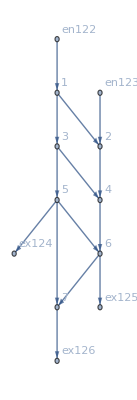

```mathematica
MFGEquations["criticalreduced1"][[2]]
MFGEquations["FG"]
```

```mathematica
MFGEquations["EqAll"]/.(MFGEquations["criticalreduced1"][[2]])
```

True

```mathematica
MFGEquations["EqAllAll"]
```

NonNegative[j998]&&NonNegative[j999]&&NonNegative[j1000]&&NonNegative[j1001]&&NonNegative[j1002]&&NonNegative[j1003]&&NonNegative[j1004]&&NonNegative[j1005]&&NonNegative[j1006]&&NonNegative[j1007]&&NonNegative[j1008]&&NonNegative[j1009]&&NonNegative[j1010]&&NonNegative[j1011]&&NonNegative[j1012]&&NonNegative[j1013]&&NonNegative[j1014]&&NonNegative[j1015]&&NonNegative[j1016]&&NonNegative[j1017]&&NonNegative[j1018]&&NonNegative[j1019]&&NonNegative[j1020]&&NonNegative[j1021]&&NonNegative[j1022]&&NonNegative[j1023]&&NonNegative[j1024]&&NonNegative[j1025]&&NonNegative[jt1026]&&NonNegative[jt1027]&&NonNegative[jt1028]&&NonNegative[jt1029]&&NonNegative[jt1030]&&NonNegative[jt1031]&&NonNegative[jt1032]&&NonNegative[jt1033]&&NonNegative[jt1034]&&NonNegative[jt1035]&&NonNegative[jt1036]&&NonNegative[jt1037]&&NonNegative[jt1038]&&NonNegative[jt1039]&&NonNegative[jt1040]&&NonNegative[jt1041]&&NonNegative[jt1042]&&NonNegative[jt1043]&&NonNegative[jt1044]&&NonNegative[jt1045]&&NonNegative[jt1046]&&NonNegative[jt1047]&&NonNegative[jt1048]&&NonNegative[jt1049]&&NonNegative[jt1050]&&NonNegative[jt1051]&&NonNegative[jt1052]&&NonNegative[jt1053]&&NonNegative[jt1054]&&NonNegative[jt1055]&&NonNegative[jt1056]&&NonNegative[jt1057]&&NonNegative[jt1058]&&NonNegative[jt1059]&&NonNegative[jt1060]&&NonNegative[jt1061]&&NonNegative[jt1062]&&NonNegative[jt1063]&&NonNegative[jt1064]&&NonNegative[jt1065]&&NonNegative[jt1066]&&NonNegative[jt1067]&&NonNegative[jt1068]&&NonNegative[jt1069]&&NonNegative[jt1070]&&NonNegative[jt1071]&&NonNegative[jt1072]&&NonNegative[jt1073]&&NonNegative[jt1074]&&NonNegative[jt1075]&&NonNegative[jt1076]&&NonNegative[jt1077]&&NonNegative[jt1078]&&NonNegative[jt1079]&&j1012==jt1026+jt1027&&j1013==jt1028+jt1029&&j1010==jt1030+jt1031&&j998==jt1032+jt1033&&j1014==jt1034+jt1035&&j1011==jt1036+jt1037&&j999==jt1038+jt1039&&j1015==jt1040+jt1041&&j1016==jt1042+jt1043&&j1000==jt1044+jt1045&&j1001==jt1046+jt1047&&j1017==jt1048+jt1049&&j1002==jt1050+jt1051+jt1052&&j1018==jt1053+jt1054+jt1055&&j1019==jt1056+jt1057+jt1058&&j1020==jt1059+jt1060+jt1061&&j1003==jt1062+jt1063+jt1064&&j1004==jt1065+jt1066+jt1067&&j1021==jt1068+jt1069+jt1070&&j1022==jt1071+jt1072+jt1073&&j1005==jt1074+jt1075&&j1007==jt1076+jt1077&&j1023==jt1078+jt1079&&j998==jt1028+jt1030&&j999==jt1026+jt1031&&j1024==jt1027+jt1029&&j1012==jt1034+jt1036&&j1000==jt1032+jt1037&&j1025==jt1033+jt1035&&j1013==jt1040+jt1042&&j1001==jt1038+jt1043&&j1002==jt1039+jt1041&&j1014==jt1046+jt1048&&j1015==jt1044+jt1049&&j1003==jt1045+jt1047&&j1016==jt1053+jt1056+jt1059&&j1004==jt1050+jt1057+jt1060&&j1005==jt1051+jt1054+jt1061&&j1006==jt1052+jt1055+jt1058&&j1017==jt1065+jt1068+jt1071&&j1018==jt1062+jt1069+jt1072&&j1007==jt1063+jt1066+jt1073&&j1008==jt1064+jt1067+jt1070&&j1019==jt1076+jt1078&&j1021==jt1074+jt1079&&j1009==jt1075+jt1077&&j1010==1&&j1011==2&&u1102==1&&u1104==2&&u1105==0&&u1081≥u1106&&u1080==u1081&&u1094≥u1107&&u1082==u1094&&u1084==u1095&&u1083==u1095&&u1096==u1097&&u1085==u1096&&u1088≥u1098&&u1087==u1098&&u1086==u1098&&u1090≥u1100&&u1099==u1100&&u1089==u1100&&u1091≥u1103&&u1101==u1103&&-u1092+u1106==0&&-u1093+u1107==0&&-u1088+u1102==0&&-u1090+u1104==0&&-u1091+u1105==0&&(j1012==0||j998==0)&&(j1013==0||j999==0)&&(j1014==0||j1000==0)&&(j1015==0||j1001==0)&&(j1016==0||j1002==0)&&(j1017==0||j1003==0)&&(j1018==0||j1004==0)&&(j1019==0||j1005==0)&&(j1020==0||j1006==0)&&(j1021==0||j1007==0)&&(j1022==0||j1008==0)&&(j1023==0||j1009==0)&&(j1024==0||j1010==0)&&(j1025==0||j1011==0)&&(jt1026==0||jt1028==0)&&(jt1027==0||jt1030==0)&&(jt1029==0||jt1031==0)&&(jt1032==0||jt1034==0)&&(jt1033==0||jt1036==0)&&(jt1035==0||jt1037==0)&&(jt1038==0||jt1040==0)&&(jt1039==0||jt1042==0)&&(jt1041==0||jt1043==0)&&(jt1044==0||jt1046==0)&&(jt1045==0||jt1048==0)&&(jt1047==0||jt1049==0)&&(jt1050==0||jt1053==0)&&(jt1051==0||jt1056==0)&&(jt1052==0||jt1059==0)&&(jt1054==0||jt1057==0)&&(jt1055==0||jt1060==0)&&(jt1058==0||jt1061==0)&&(jt1062==0||jt1065==0)&&(jt1063==0||jt1068==0)&&(jt1064==0||jt1071==0)&&(jt1066==0||jt1069==0)&&(jt1067==0||jt1072==0)&&(jt1070==0||jt1073==0)&&(jt1074==0||jt1076==0)&&(jt1075==0||jt1078==0)&&(jt1077==0||jt1079==0)&&(jt1026==0||-u1080+u1081==0)&&jt1027==0&&(jt1028==0||u1080-u1081==0)&&jt1029==0&&(jt1030==0||u1080-u1106==0)&&(jt1031==0||u1081-u1106==0)&&(jt1032==0||u1082-u1094==0)&&jt1033==0&&(jt1034==0||-u1082+u1094==0)&&jt1035==0&&(jt1036==0||u1094-u1107==0)&&(jt1037==0||u1082-u1107==0)&&(jt1038==0||u1083-u1095==0)&&(jt1039==0||u1084-u1095==0)&&(jt1040==0||-u1083+u1095==0)&&(jt1041==0||-u1083+u1084==0)&&(jt1042==0||-u1084+u1095==0)&&(jt1043==0||u1083-u1084==0)&&(jt1044==0||-u1096+u1097==0)&&(jt1045==0||u1085-u1096==0)&&(jt1046==0||u1096-u1097==0)&&(jt1047==0||u1085-u1097==0)&&(jt1048==0||-u1085+u1096==0)&&(jt1049==0||-u1085+u1097==0)&&(jt1050==0||u1086-u1098==0)&&(jt1051==0||u1087-u1098==0)&&(jt1052==0||u1088-u1098==0)&&(jt1053==0||-u1086+u1098==0)&&(jt1054==0||-u1086+u1087==0)&&(jt1055==0||-u1086+u1088==0)&&(jt1056==0||-u1087+u1098==0)&&(jt1057==0||u1086-u1087==0)&&(jt1058==0||-u1087+u1088==0)&&jt1059==0&&jt1060==0&&jt1061==0&&(jt1062==0||-u1099+u1100==0)&&(jt1063==0||u1089-u1099==0)&&(jt1064==0||u1090-u1099==0)&&(jt1065==0||u1099-u1100==0)&&(jt1066==0||u1089-u1100==0)&&(jt1067==0||u1090-u1100==0)&&(jt1068==0||-u1089+u1099==0)&&(jt1069==0||-u1089+u1100==0)&&(jt1070==0||-u1089+u1090==0)&&jt1071==0&&jt1072==0&&jt1073==0&&(jt1074==0||-u1101+u1103==0)&&(jt1075==0||u1091-u1101==0)&&(jt1076==0||u1101-u1103==0)&&(jt1077==0||u1091-u1103==0)&&jt1078==0&&jt1079==0

```mathematica
Chop/@(MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]])
```

<|{2,1->2}→0,{3,1->3}→2,{4,2->4}→2,{4,3->4}→0,{5,3->5}→2,{6,4->6}→2,{6,5->6}→0,{7,5->7}→0,{ex1475,5->ex1475}→2,{7,6->7}→0,{ex1476,6->ex1476}→2,{ex1477,7->ex1477}→0,{1,en1473->1}→2,{2,en1474->2}→2,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{3,3->5}→0,{4,4->6}→0,{5,5->6}→0,{5,5->7}→0,{5,5->ex1475}→0,{6,6->7}→0,{6,6->ex1476}→0,{7,7->ex1477}→0,{en1473,en1473->1}→0,{en1474,en1474->2}→0|>

#### Non-linear case

```mathematica
alpha = .99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,2.4},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{1-0.1,4.7},GridLines->Automatic]&/@MFGEquations["BEL"]
```